# MAP-Elites Algorithm

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

## Define functions

```mathematica
LaunchKernels[8];
ObjectiveFunction[X_] := Module[{performance,attribute},
(*Define a objective function to map input (X) to a performance and attribute space (Y)*)
performance = Total[X,{2}];
attribute = Round[X⟦All,1⟧/0.1];
Return[Transpose[{performance,attribute}]]
]

IntializePool[X_,Y_]:=Module[{pool,indexes,Xtemp,Ytemp,Maxindex,Sample},
(*create the initial pool according to the attribute*)
pool = {};
Table[
indexes =Flatten[Position[Y⟦All,-1⟧,attributeIndex]];
Xtemp = X⟦indexes⟧;
Ytemp = Y⟦indexes⟧;
Maxindex = Ordering[Ytemp⟦All,1⟧]⟦-1⟧;
Sample = Join[Xtemp⟦Maxindex⟧,Ytemp⟦Maxindex⟧];
AppendTo[pool,Sample],
{attributeIndex,DeleteDuplicates[Y⟦All,-1⟧]}];
Return[pool];
]
CrossOver[pool_,featureNum_]:=Module[{indexes,offspring},
indexes =RandomInteger[{1,Length[pool]},2] ;
(*Print[pool⟦indexes⟧//MatrixForm];*)
offspring = Table[Flatten[pool⟦indexes⟦RandomInteger[{1,2},1]⟧⟧]⟦i⟧,{i,featureNum}];
(*Print[offspring];*)
Return[offspring]
]
Mutation[offspringOrgi_,sigma_]:=Module[{indexes,offspring},
offspring = offspringOrgi+RandomVariate[NormalDistribution[0,sigma],{Length[offspringOrgi]}];
Return[offspring]
]
```

```mathematica
GenerateSamples[pool_,featureNum_,sigma_,mutationRate_,{batchSizeC_,batchSizeM_,batchSizeR_}]:=Module[{samples,offspring},
samples = {};
(*Crossover + Mutation*)
Table[
offspring = CrossOver[pool,featureNum];
If[RandomReal[]<mutationRate,
offspring = Mutation[offspring,sigma]
];
AppendTo[samples,offspring],
{i,batchSizeC}];
(*Mutation*)
Table[
offspring = pool⟦RandomInteger[{1,Length[pool]}]⟧⟦1;;featureNum⟧;
offspring = Mutation[offspring,sigma];
AppendTo[samples,offspring],
{i,batchSizeM}];
(*Random sampling*)
Table[
offspring =Flatten[RandomReal[{0,1},{1,featureNum}]]; 
AppendTo[samples,offspring],
{i,batchSizeR}];
Return[samples]
]
```

```mathematica
UpdatePool[samples_,pool_]:=Module[{indexes,poolindexes,poolelite,samplesTemp,Maxindex,elite,originalpool},
originalpool=pool;
Table[
indexes =Flatten[Position[samples⟦All,-1⟧,attributeIndex]];
poolindexes =Flatten[Position[pool⟦All,-1⟧,attributeIndex]];
poolelite = Flatten[pool⟦poolindexes⟧];
samplesTemp = samples⟦indexes⟧;
Maxindex = Ordering[samplesTemp⟦All,-2⟧]⟦-1⟧;
elite = Flatten[samplesTemp⟦Maxindex⟧];
Which[Length[poolindexes]<1,
AppendTo[originalpool,elite],
elite⟦-2⟧>poolelite⟦-2⟧,
originalpool⟦poolindexes⟧ = elite
],
{attributeIndex,DeleteDuplicates[samples⟦All,-1⟧]}];
Return[originalpool]
]
```

```mathematica
fromXtoSpectrum1[X_,Qset_]:=Module[{gridweights,standardD,spectrum,griddistance},
griddistance = Table[((X⟦1⟧-i)^2+(X⟦2⟧-j)^2+(X⟦3⟧-k)^2)^(1/2),{i,Subdivide[0,1,(Dimensions@shapes)⟦1⟧-1]},{j,Subdivide[0,1,(Dimensions@shapes)⟦2⟧-1]},{k,Subdivide[0,1,(Dimensions@shapes)⟦3⟧-1]}];
gridweights =N[PDF[NormalDistribution[0,0.0001+0.08*X⟦4⟧],griddistance]];
If[Total[Flatten[gridweights]]>0,
gridweights = gridweights/Total[Flatten[gridweights]]];
spectrum = 0;
Table[spectrum = spectrum +gridweights⟦i,j,k⟧*Qset⟦i,j,k,All⟧,{i,1,(Dimensions@gridweights)⟦1⟧},{j,1,(Dimensions@gridweights)⟦2⟧},{k,1,(Dimensions@gridweights)⟦3⟧}];
Return[spectrum]
]
```

```mathematica
fromXtoSpectrum2[X_,Qset_]:=Module[{gridweights,standardD,spectrum,griddistance},

spectrum =(1-X⟦4⟧)*Qset⟦Round[X⟦1⟧/(1/8)]+1,Round[X⟦2⟧/(1/10)]+1,Round[X⟦3⟧/(1/10)]+1,All⟧ +X⟦4⟧Qset⟦1,1,1,All⟧;
Return[spectrum]
]
```

```mathematica
fromSpetrumtoY[data_]:=Module[{rescaleddata,peaks,prominences,class,fitness,boundary1,boundary2,fitness1,fitness2,function,figure},
rescaleddata = Rescale[data];
peaks = FindPeaks[rescaleddata];
peaks⟦All,1⟧ = Round[peaks⟦All,1⟧ ];
prominences = Prominence[wavelength,rescaleddata,peaks];
peaks = peaks⟦Flatten[Position[prominences,_?(#>0.01&)]]⟧;
prominences = prominences⟦Flatten[Position[prominences,_?(#>0.01&)]]⟧;
If[Length[prominences] ==0,Return[{0,False}]];
Which[Length[prominences] ==1,
class = Ceiling[(wavelength⟦peaks⟦1⟧⟦1⟧⟧ - Min[wavelength])/0.05];
fitness =1/Total[rescaleddata] Total[rescaleddata⟦Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦1⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦1⟧⟦1⟧⟧ +0.05&]⟧] ,
Length[prominences] ≥2,
peaks = peaks⟦Ordering[prominences,-2]⟧;
prominences = prominences⟦Ordering[prominences,-2]⟧;
class =Ceiling[(wavelength⟦peaks⟦All,1⟧⟧ - Min[wavelength])/0.05];
boundary1 = Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦1⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦1⟧⟦1⟧⟧ +0.05&];
boundary2 = Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦2⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦2⟧⟦1⟧⟧ +0.05&];
fitness1 =Total[rescaleddata⟦Union[boundary1,boundary2]⟧]/Total[rescaleddata];
fitness2= Total[rescaleddata⟦boundary2⟧]/Total[rescaleddata];
];
function = Interpolation[Transpose[{wavelength,rescaleddata}]];
figure = ListLinePlot[Transpose[{wavelength,rescaleddata}],PlotStyle->Directive[Blue],Epilog->{Red,Table[Line[{{i⟦1⟧,0},i}],{i,Transpose[{wavelength⟦peaks⟦All,1⟧⟧,peaks⟦All,2⟧}]}]},PlotRange->All];
Which[Length[prominences] ==1,
Return[{1,figure,fitness,class}],
Length[prominences] ≥2,
Return[{2,figure,{fitness1,fitness2},class}]
]
]
Prominence[wavelength_,rescaleddata_,peaks_]:=Module[{function,plot,prominences,solutions,leftBasis,rightBasis,leftwavelengths,rightwavelengths,leftHeight,rightHeight,prominence},
function = Interpolation[Transpose[{wavelength,rescaleddata}]];
prominences = 
Table[
plot = Plot[function[x],{x,Min[wavelength],Max[wavelength]},Mesh->{{peaks⟦i⟧⟦2⟧}},MeshFunctions->{#2&},MeshStyle->PointSize[Medium],PlotRange->All,PlotPoints->10000];
solutions=Sort@Cases[Normal@plot,Point[{x_,y_}]->x,Infinity];
solutions = DeleteCases[solutions,x_/;Abs[x -wavelength⟦peaks⟦i⟧⟦1⟧⟧]≤0.01];
leftBasis =Max[Max[ DeleteCases[solutions,x_/;x>wavelength⟦peaks⟦i⟧⟦1⟧⟧]],Min[wavelength]];
rightBasis = Min[Min[DeleteCases[solutions,x_/;x<wavelength⟦peaks⟦i⟧⟦1⟧⟧]],Max[wavelength]];
leftwavelengths= Select[wavelength,leftBasis≤#≤wavelength⟦peaks⟦i⟧⟦1⟧⟧&];
rightwavelengths=Select[wavelength,wavelength⟦peaks⟦i⟧⟦1⟧⟧≤#≤rightBasis&] ;
leftHeight=Min[function[leftwavelengths]];
rightHeight=Min[function[rightwavelengths]];
prominence = Min[peaks⟦i⟧⟦2⟧ - leftHeight,peaks⟦i⟧⟦2⟧ - rightHeight],{i,Length[peaks]}];
Return[prominences]]
```

```mathematica
ObjectiveFunction2[X_,Qset_]:=Module[{data,Y,results,XNew,YNew,figures},
data = Table[fromXtoSpectrum2[X⟦i⟧,Qset],{i,(Dimensions@X)⟦1⟧}];
Y = Table[
fromSpetrumtoY[data⟦j⟧],{j,Length[data]}];
results = {};
Table[
Which[
(*Y⟦i⟧⟦1⟧ ==1,
AppendTo[results,{X⟦i⟧,Y⟦i⟧}],*)
Y⟦i⟧⟦1⟧ ==2,
AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦2⟧,Y⟦i⟧⟦4⟧⟦2⟧}]}]
(*AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦1⟧,100*Y⟦i⟧⟦4⟧⟦1⟧+Y⟦i⟧⟦4⟧⟦2⟧}]}];
AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦2⟧,10000*Y⟦i⟧⟦4⟧⟦1⟧+Y⟦i⟧⟦4⟧⟦2⟧}]}]*)],{i,Length[Y]}];
XNew = results⟦All,1⟧;
YNew = results⟦All,2⟧⟦All,-2;;⟧;
figures = results⟦All,2⟧⟦All,-3⟧;
Return[{XNew,YNew,figures}]
]
```

## Run tests

```mathematica
randomseed= 100;
SeedRandom[randomseed];
```

```mathematica
shapes = ParallelTable[ToString[k]<>"_"<>ToString[i]<>"_"<>ToString[j],{k,20,60,5},{i,1,3,0.2},{j,1,3,0.2}];
randomshapes = shapes;
wavelength=Table[i,{i,0.4,0.9,0.4/999}];
```

```mathematica
Qset = Import[NotebookDirectory[]<>"Qset.mx"]; (*Read in the spectral data of Au nanostructures*)
```

```mathematica
featureNum = 4; (* the number of feature of the input space*)
initialNum = 10; (* the initial sampling number*)
batchSizeC = 10;(* crossover+ mutation *)
batchSizeM = 10; (* mutation *)
batchSizeR = 3;(* random sampling*)
sigma = 0.08;(* the standard deviation of noise in mutation *)
mutationRate = 0.4;(* the probability of mutation *)
X = RandomReal[{0,1},{initialNum,featureNum}]; 
results = ObjectiveFunction2[X,Qset];
X = results⟦1⟧;
Y = results⟦2⟧;
pool = IntializePool[X,Y];
Initialpool=pool;
```

```mathematica
MAPResults=ParallelTable[
pool = Initialpool;
Observations = {};
AppendTo[Observations, Join[X,Y,2]];
SeedRandom[count];
poolSet = Table[
samplesInput= GenerateSamples[pool,featureNum,sigma,mutationRate,{batchSizeC,batchSizeM,batchSizeR}];
samplesInput = samplesInput/.n_?NumericQ/;n>1->1;
samplesInput = samplesInput/.n_?NumericQ/;n<0->0;
sampleResult = ObjectiveFunction2[samplesInput,Qset];
samplesInput = sampleResult⟦1⟧;
sampleResult = sampleResult⟦2⟧;
samples = Join[samplesInput,sampleResult,2];
AppendTo[Observations,samples];
pool=UpdatePool[samples,pool],{i,50}];
{Observations,Join[{Initialpool},poolSet]},{count,16}];
```

```mathematica
RandomResults=ParallelTable[
pool = Initialpool;
Observations = {};
AppendTo[Observations, Join[X,Y,2]];
SeedRandom[100*count];
poolSet = Table[
samplesInput=RandomReal[{0,1},{Total[{batchSizeC,batchSizeM,batchSizeR}],featureNum}];
samplesInput = samplesInput/.n_?NumericQ/;n>1->1;
samplesInput = samplesInput/.n_?NumericQ/;n<0->0;
sampleResult = ObjectiveFunction2[samplesInput,Qset];
samplesInput = sampleResult⟦1⟧;
sampleResult = sampleResult⟦2⟧;
samples = Join[samplesInput,sampleResult,2];
AppendTo[Observations,samples];
pool=UpdatePool[samples,pool],{i,50}];
{Observations,Join[{Initialpool},poolSet]},{count,16}];
```

```mathematica
Export[NotebookDirectory[]<>"MAPResults"<>".mx",MAPResults];
Export[NotebookDirectory[]<>"RandomResults"<>".mx",RandomResults];
```

```mathematica
MAPResultsTotal = Import[NotebookDirectory[]<>"MAPResults"<>".mx"];
RandomResultsTotal =Import[NotebookDirectory[]<>"RandomResults"<>".mx"];
MAPResults = MAPResultsTotal⟦All,2,All⟧;
RandomResults=RandomResultsTotal⟦All,2,All⟧;
```

```mathematica
mean1 = Table[Table[Mean[MAPResults⟦i⟧⟦j⟧⟦All,-2⟧],{j,(Dimensions@MAPResults)⟦2⟧}],{i,Length[MAPResults]}];
Table[Length[MAPResults⟦i⟧⟦-1⟧],{i,Length[MAPResults]}]
meanoversamples1 = Table[Around[mean1⟦All,i⟧],{i,(Dimensions@MAPResults)⟦2⟧}];
meanoversamples1MEAN = Table[Mean[mean1⟦All,i⟧],{i,(Dimensions@MAPResults)⟦2⟧}];
meanoversamples1STD = Table[StandardDeviation[mean1⟦All,i⟧],{i,(Dimensions@MAPResults)⟦2⟧}];
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
mean2 = Table[Table[Mean[RandomResults⟦i⟧⟦j⟧⟦All,-2⟧],{j,(Dimensions@RandomResults)⟦2⟧}],{i,Length[RandomResults]}];
Table[Length[MAPResults⟦i⟧⟦-1⟧],{i,Length[MAPResults]}]
meanoversamples2 =  Table[Around[mean2⟦All,i⟧],{i,(Dimensions@RandomResults)⟦2⟧}];
meanoversamples2MEAN = Table[Mean[mean2⟦All,i⟧],{i,(Dimensions@RandomResults)⟦2⟧}];
meanoversamples2STD = Table[StandardDeviation[mean2⟦All,i⟧],{i,(Dimensions@RandomResults)⟦2⟧}];
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
l1 = Table[Table[Length[MAPResults⟦j⟧⟦i⟧],{i,(Dimensions@MAPResults)⟦2⟧}],{j,(Dimensions@MAPResults)⟦1⟧}];
meanl1=Table[Around[l1⟦All,i⟧],{i,(Dimensions@MAPResults)⟦2⟧}];
meanl1MEAN = Table[Mean[l1⟦All,i⟧],{i,(Dimensions@MAPResults)⟦2⟧}];
meanl1STD = Table[StandardDeviation[l1⟦All,i⟧],{i,(Dimensions@MAPResults)⟦2⟧}];
l2 = Table[Table[Length[RandomResults⟦j⟧⟦i⟧],{i,(Dimensions@RandomResults)⟦2⟧}],{j,(Dimensions@RandomResults)⟦1⟧}];
meanl2=Table[Around[l2⟦All,i⟧],{i,(Dimensions@RandomResults)⟦2⟧}];
meanl2MEAN = Table[Mean[l2⟦All,i⟧],{i,(Dimensions@RandomResults)⟦2⟧}];
meanl2STD = Table[StandardDeviation[l2⟦All,i⟧],{i,(Dimensions@RandomResults)⟦2⟧}];
```

```mathematica
spectrums = Table[Transpose[{wavelength,Rescale[fromXtoSpectrum2[i,Qset]]}],{i,SortBy[MAPResults⟦8⟧⟦-1⟧⟦All⟧,Last]⟦All,1;;4⟧}];
lineStyle = {Thick, Gray, Dashed};
lines = Table[Line[{{0.4+0.05i,0},{0.4+0.05i,1}}],{i,10}];
```

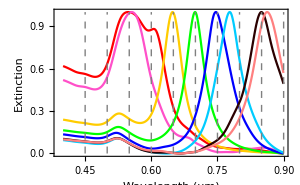

/home/group/scapa/group/Yibin Jiang/Projects/Nanobot2/Nanobot_Experiment/test_Algorithm/MAP_elite/Toy1/MAP_elite_mathematica/UV-Vis_example.svg

```mathematica
f =ListLinePlot[spectrums,PlotRange->Full,AspectRatio->1/GoldenRatio,Epilog->{Directive[lineStyle],lines},PlotStyle->{RGBColor[1,0,0],
RGBColor[255/255,80/255,201/255],RGBColor[255/255,204/255,0/255],RGBColor[0/255,255/255,0/255],RGBColor[0/255,0/255,255/255],RGBColor[0/255,204/255,255/255],RGBColor[43/255,0/255,0/255],RGBColor[255/255,128/255,128/255]},PlotRange->{{Min[wavelength],Max[wavelength]},{0,1}},Frame-> True,FrameLabel->{"Wavelength (μm)","Extinction"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},FrameStyle->{{Thick,Thick},{Thick,Thick}},ImageSize->300,FrameTicksStyle->{{Thick,Thick},{Thick,Thick}}]
Export[NotebookDirectory[]<>"UV-Vis_example.svg",f,ImageResolution->500]
```

## Plot the whole phase space according to the shape and the mixture rate

```mathematica
spectrumAll =ParallelTable[
Qtemp = Qset⟦i,j,k,All⟧;
Table[
spectrum =(1-mixturerate)Qtemp+mixturerate Qset⟦1,1,1,All⟧,
{mixturerate,0,1,0.05}],{i,1,(Dimensions@randomshapes)⟦1⟧},{j,1,(Dimensions@randomshapes)⟦2⟧},{k,1,(Dimensions@randomshapes)⟦3⟧}];
Export[NotebookDirectory[]<>"SpectrumAll"<>ToString[randomseed]<>".mx",spectrumAll];
```

```mathematica
spectrumAll = Import[NotebookDirectory[]<>"SpectrumAll"<>ToString[randomseed]<>".mx"];
```

```mathematica
(*Grid search to find the upper boundaries*)
resultsAll = ParallelTable[
Table[
spectrum = spectrumAll⟦i,j,k,mixturerate⟧;
fromSpetrumtoY[spectrum],
{mixturerate,1,21}],{i,1,(Dimensions@randomshapes)⟦1⟧},{j,1,(Dimensions@randomshapes)⟦2⟧},{k,1,(Dimensions@randomshapes)⟦3⟧}];
Export[NotebookDirectory[]<>"resultsAll"<>ToString[randomseed]<>".mx",resultsAll];
```

```mathematica
resultsAll = Import[NotebookDirectory[]<>"resultsAll100"<>".mx"];
```

```mathematica
maxfitness = Table[
classAndfitness= Table[
If[resultsAll⟦i,j,k,mixturerate⟧⟦1⟧==2 && resultsAll⟦i,j,k,mixturerate⟧⟦4,2⟧==classindex,
resultsAll⟦i,j,k,mixturerate⟧⟦3,2⟧,
-100],
{i,1,(Dimensions@randomshapes)⟦1⟧},
{j,1,(Dimensions@randomshapes)⟦2⟧},
{k,1,(Dimensions@randomshapes)⟦3⟧},
{mixturerate,1,21}];
Max[Flatten[classAndfitness]],{classindex,3,10}];
```

```mathematica
Mean[maxfitness]
```

0.602725

```mathematica
ClearAll[deviationslLLP]
deviationslLLP[ave_,dev_,opts:OptionsPattern[]]:=Module[{
fill=Join@@(Thread[Range[Length@ave]->List/@(Length[ave] #+Range[Length@ave])]&/@{1,2}),apd=Style[#,Opacity[0]]&/@(ave+dev),
amd=Style[#,Opacity[0]]&/@(ave-dev),p1,p2},
p1=ListLinePlot[Join@@{ave,apd,amd},Filling->fill,opts]
]
```

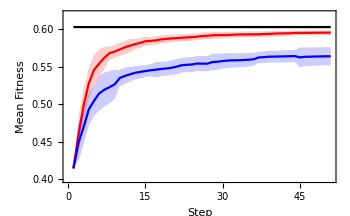

```mathematica
f1 = deviationslLLP[{meanoversamples1MEAN},{meanoversamples1STD},PlotStyle->{Red},PlotRange->{0.4,0.62},AspectRatio->1/GoldenRatio,PlotLegends->Placed[{"MAP-Elites"},{Right,0.3}]];
f12 = ListLinePlot[meanoversamples1MEAN,PlotStyle->{Red},PlotLegends->Placed[{"MAP-Elites"},{Right,0.3}],PlotRange->{0.4,0.62}];
f1 = f1;
f2 =deviationslLLP[{meanoversamples2MEAN},{meanoversamples2STD},PlotStyle->{Blue},PlotRange->{0.4,0.62},PlotLegends->Placed[{"Random"},{Right,0.3}]];
f22=ListLinePlot[meanoversamples2MEAN,PlotStyle->{Blue},PlotLegends->Placed[{"Random"},{Right,0.3}],PlotRange->{0.4,0.62}];
f2 =f2;
f3 =ListLinePlot[Table[Mean[maxfitness],{i,Length@meanoversamples2}],PlotStyle->{Black},PlotLegends->Placed[{"Upper Boundary"},{Right,0.3}],PlotRange->{0.4,0.62}];
 p = Show[{f1,f2,f3},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},FrameLabel->{"Step","Mean Fitness"},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},FrameTicksStyle->{{Thick,Thick},{Thick,Thick}},ImageSize->350]
Export[NotebookDirectory[]<>"mean_fitness_50_steps_random.png",p,ImageResolution->500];
Export[NotebookDirectory[]<>"mean_fitness_50_steps_random.svg",p,ImageResolution->500];
```

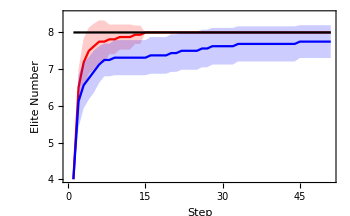

```mathematica
f1 = deviationslLLP[{meanl1MEAN},{meanl1STD},PlotStyle->{Red},PlotRange->{4,8.5},AspectRatio->1/GoldenRatio,PlotLegends->Placed[{"MAP-Elites"},{Right,0.3}]];
f12 = ListLinePlot[meanl1MEAN,PlotStyle->{Red},PlotLegends->Placed[{"MAP-Elites"},{Right,0.3}],PlotRange->{4,8.5}];
f1 = f1;
f2 = deviationslLLP[{meanl2MEAN},{meanl2STD},PlotStyle->{Blue},PlotRange->{4,8.5},PlotLegends->Placed[{"Random"},{Right,0.3}]];
f22 = ListLinePlot[meanl2MEAN,PlotStyle->{Blue},PlotLegends->Placed[{"Random"},{Right,0.3}],PlotRange->{4,8.5}];
f2=f2;
f3 =ListLinePlot[Table[8,{i,Length@meanoversamples2}],PlotStyle->{Black},PlotLegends->Placed[{"Upper Boundary"},{Right,0.3}],PlotRange->{4,8.5}];
 p = Show[{f1,f2,f3},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},FrameLabel->{"Step","Elite Number"},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},FrameTicksStyle->{{Thick,Thick},{Thick,Thick}},ImageSize->350]
Export[NotebookDirectory[]<>"mean_elites_50_steps_random.png",p,ImageResolution->500];
Export[NotebookDirectory[]<>"mean_elites_50_steps_random.svg",p,ImageResolution->500];
```